## Analytic EWS for Ricker model

## Bifurcation diagram: Ricker model

```mathematica
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
SetDirectory["/Users/tbury/Google Drive/Research/doctorate/critical_transitions_18/ews_seasonal/models_ricker/ricker_std"];
```

```mathematica
(* Import bifurcation data points *)
bifDataRb= Import["bifurcation/data/r_vary.csv"]; (* varing r *)
```

```mathematica
(* Figure parameters *)
ps = 0.004;
```

### Varying rb

```mathematica
bifDataRb[[1]]
```

{,Time,Pop,r}

```mathematica
pData=bifDataRb[[2;;,{4,3}]];
```

```mathematica
extPts=Table[{r,0},{r,-0.2,0,0.01}];
```

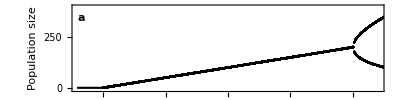

```mathematica
bifPlot=ListPlot[{pData,extPts},
LabelStyle->ls,
PlotRange->{{-0.2,2.2},{-10,400}},
PlotStyle->Directive[{Black,PointSize[ps]}],
Frame->{{True,True},{True,True}},
FrameLabel->{{"Population size",""},{"",""}},
FrameTicks->{{Automatic,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aRatio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["a",letls,Bold],labelPos]}]
```

## Import data

```mathematica
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
SetDirectory["/Users/tbury/Google Drive/Research/doctorate/critical_transitions_18/ews_seasonal/models_ricker/ricker_std"];
```

### General figure parameters

```mathematica
(* plot range for r *)
xRange={0,1.8};
```

```mathematica
(* Label style *)
ls=11;
```

```mathematica
(* Letter label style *) 
letls=11;
```

```mathematica
imgs=400;
aRatio=0.25;
padding={{60,60},{20,20}};
{{padLeft,padRight},{padBottom,padTop}}=padding;
lt=0.006;
labelPos=Scaled[{0.03,0.85}];
```

```mathematica
rVals=Union[dfEws[[2;;,1]]];
rMax=Max[rVals];
rPlotRange={-0.2,2.2};
```

## Plot of S(ω)/Var

```mathematica
rVals=Range[0.2,1.8,0.4];
```

```mathematica
rVals
```

{0.2,0.6,1.,1.4,1.8}

```mathematica
Clear[colFun1]
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
cols=Reverse[Table[colFun1[i],{i,0.1,1,1/Length[rVals ]}]]
```

{RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.5, 0.25, 0.5],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.1, 0.05, 0.9]}

```mathematica
legend=LineLegend[cols,Table["r="<>ToString[i],{i,rVals}],Spacings->{0,0},LabelStyle->11]
```

```mathematica
cols
```

{RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.5, 0.25, 0.5],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.1, 0.05, 0.9]}

```mathematica
Clear[specAnal]
specAnal[ω_,r_,σ_]:=(1/(2*Pi))*(r*(2-r)/(1+(1-r)^2-2*(1-r)*Cos[ω]));
```

```mathematica
(* Table of power spectrum values normalised by variance *)
specPlotData=Table[Cases[dfPspec,{rval,_,_}][[;;,{2,3}]],{rval,rValsPlot}];
```

```mathematica
Table[specAnal[ω,r,0.1],{r,rVals}]
```

{0.0572958/(1.64-1.6 Cos[ω]),0.13369/(1.16-0.8 Cos[ω]),0.159155,0.13369/(1.16+0.8 Cos[ω]),0.0572958/(1.64+1.6 Cos[ω])}

```mathematica
cols
```

{RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.5, 0.25, 0.5],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.1, 0.05, 0.9]}

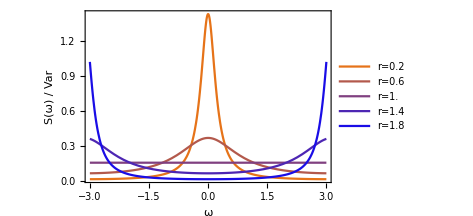

```mathematica
pspecPlot=Plot[Evaluate[Table[specAnal[ω,r,0.1],{r,rVals}]],{ω,-3,3},
PlotRange->All,
ImageSize->350,
PlotStyle->cols,
Frame->True,
LabelStyle->12,
FrameLabel->{{"S(ω) / Var",""},{"ω",""}},
PlotLegends->Placed[legend,Scaled[{0.75,0.63}]]]
```

```mathematica
Export["figures/ricker_pspec_anal.png",pspecPlot,ImageResolution->200];
```

## Plots of EWS against r

```mathematica
(* noise in terms of r *)
alpha=0.01;
sigma[r_]:=0.1*Sqrt[((r/alpha) + (r/alpha)^2)]
```

### Variance

```mathematica
legend=LineLegend[{{TMBcolours[[1]],Dashed},TMBcolours[[1]]},Style[#,9]&/@{"additive noise","multiplicative noise"},Spacings->-0.1,
LegendMarkerSize->{{25,15}}];
```

```mathematica
varFun[r_]:=sigma[r]^2/(r*(2-r));
varFunAdd[r_]:=100/(r*(2-r));
```

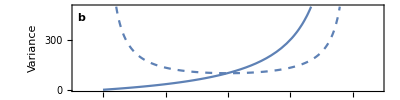

```mathematica
varPlot=Plot[{varFunAdd[r],varFun[r]},{r,0,2},
LabelStyle->ls,
PlotRange->{rPlotRange,{0,500}},
PlotStyle->{{TMBcolours[[1]],Dashed},TMBcolours[[1]]},
Frame->{{True,True},{True,True}},
FrameLabel->{{"Variance",""},{"",""}},
FrameTicks->{{Automatic,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aRatio,
PlotLegends->Placed[legend,Scaled[{0.5,0.7}]],
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["b",letls,Bold],labelPos]}
]
```

### Coefficient of variation

```mathematica
legend=LineLegend[{{TMBcolours[[2]],Dashed},TMBcolours[[2]]},Style[#,9]&/@{"additive noise","multiplicative noise"},Spacings->-0.1,
LegendMarkerSize->{{25,15}}]
```

```mathematica
cvFun[r_]:=Sqrt[varFun[r]]/(r/alpha);
cvFunAdd[r_]:=Sqrt[varFunAdd[r]]/(r/alpha)
```

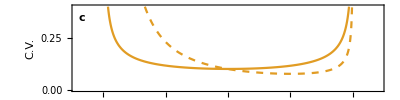

```mathematica
cvPlot=Plot[{cvFunAdd[r],cvFun[r]},{r,0,2},
LabelStyle->ls,
PlotRange->{rPlotRange,{0,0.4}},
PlotStyle->{{TMBcolours[[2]],Dashed},TMBcolours[[2]]},
Frame->{{True,True},{True,True}},
FrameLabel->{{"C.V.",""},{"",""}},
FrameTicks->{{Automatic,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aRatio,
ImagePadding->padding,
PlotLegends->Placed[legend,Scaled[{0.5,0.7}]],
Epilog->{Directive[{Black}],Text[Style["c",letls,Bold],labelPos]}
]
```

### Lag-1 Autocorrelation

```mathematica
acFun[r_,tau_]:=(1-r)^(tau)
```

```mathematica
legend=LineLegend[TMBcolours[[{4,5,7}]],Style[#,9]&/@{"lag-1","lag-2","lag-3"},Spacings->-0.1]
```

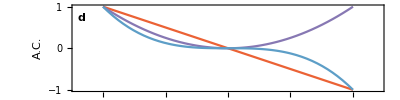

```mathematica
acPlot=Plot[Evaluate[Table[acFun[r,tau],{tau,{1,2,3}}]],{r,0,2},
LabelStyle->ls,
PlotRange->{rPlotRange,{-1,1}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"A.C.",""},{"",""}},
FrameTicks->{{Automatic,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
PlotStyle->TMBcolours[[{4,5,7}]],
PlotLegends->Placed[legend,Scaled[{0.1,0.22}]],
AspectRatio->aRatio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["d",letls,Bold],labelPos]}
]
```

### Smax/Var

```mathematica
smaxVarFun[r_]:=(1/2*Pi)*Max[r(2-r)/(1+(1-r)^2-2(1-r)), r(2-r)/(1+(1-r)^2+2(1-r))]
```

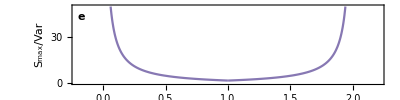

```mathematica
smaxVarPlot=Plot[smaxVarFun[r],{r,0,2},
LabelStyle->ls,
PlotRange->{rPlotRange,{0,50}},
PlotStyle->TMBcolours[[5]],
Frame->{{True,True},{True,True}},
FrameLabel->{{"S_max/Var",""},{"Growth rate, r",""}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{40,padTop}},
Epilog->{Directive[{Black}],Text[Style["e",letls,Bold],labelPos]}
]
```

## Grid all plots together

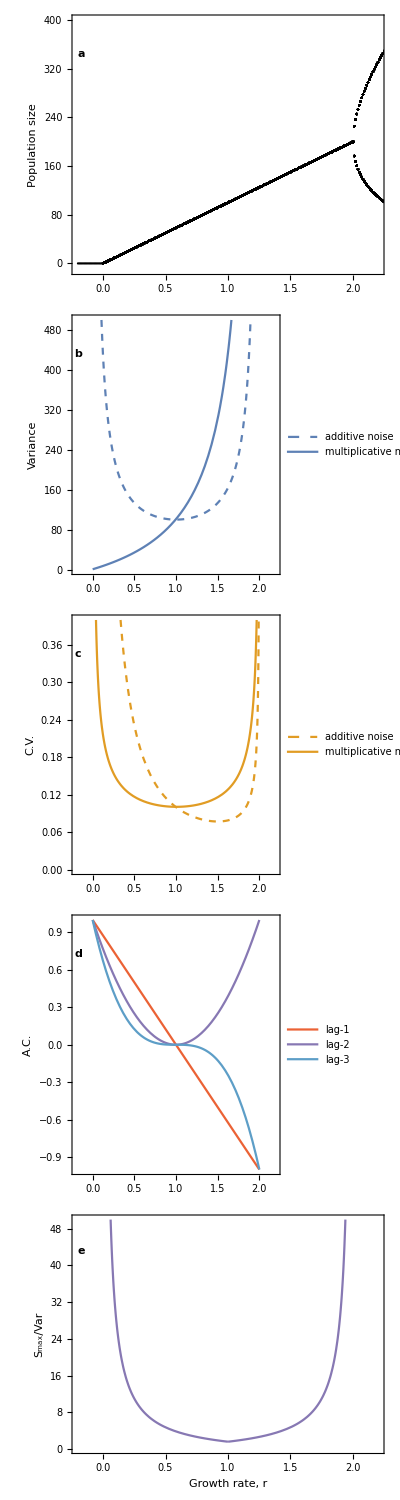

```mathematica
plotTemp=Grid[{{bifPlot},{varPlot},{cvPlot},{acPlot},{smaxVarPlot}},Spacings->{0,-2}]
```

```mathematica
Export["figures/ews_stat_ricker_analytic.png",plotTemp,ImageResolution->200];
```